```mathematica
saveDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180412/";
fSuff=".wdx";
kFiles={"Orb1612_itvl1_kappa-fixT140eV_nRolls5000"<>fSuff,"Orb1612_itvl2_kappa-fixT180eV_nRolls5000"<>fSuff};
mFiles={"Orb1612_itvl1_Maxwell-fixT120eV_nRolls5000"<>fSuff,"Orb1612_itvl2_Maxwell-fixT140eV_nRolls5000"<>fSuff};
(*These files contain kFits and gFits*)
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
minPot=200;maxPot=1400;minJ=0.4;maxJ=2.0;
plotRange={{minPot,maxPot},{minJ,maxJ}};
```

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},
If[(Length@Dimensions[l])==1,ny=1;{nx}=Dimensions[l];,{ny,nx}=Dimensions[l];];
Print[Head@l];
Print[ToString@StringForm["ny: `1`, nx: `2`",ny,nx]];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
initFitFiles={saveDir<>"itvl1_initialFits"<>fSuff,saveDir<>"itvl2_initialFits"<>fSuff};
(*These contain {kInitialFit,gInitialFit,JVParTable,jErrData,initTitle,tid,jData,jErrData,jWt,potErr,curErr,potVal,curVal}*)
```

#### Load interval=1 stuff

```mathematica
interval=1;
```

```mathematica
<<(saveDir<>kFiles[[interval]])
```

```mathematica
<<(saveDir<>mFiles[[interval]])
```

```mathematica
<<(initFitFiles[[interval]])
```

```mathematica
kInitialFit1=kInitialFit;
gInitialFit1=gInitialFit;
JVParTable1=JVParTable;
jErrData1=jErrData;
initTitle1=initTitle;
tid1=tid;
jData1=jData;
jErrData1=jErrData;
jWt1=jWt;
potErr1=potErr;
curErr1=curErr;
potVal1=potVal;
curVal1=curVal;
```

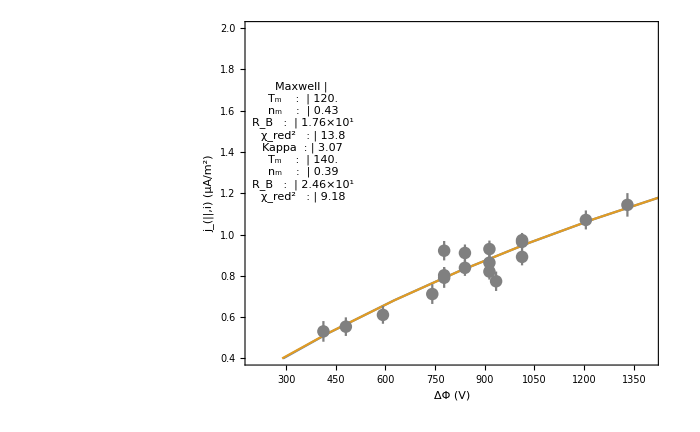

```mathematica
JVInitFitPlot1=Show[Plot[{kInitialFit1[pot],gInitialFit1[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Interval `1` (`2`)",interval,initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

#### Load interval=2 stuff

```mathematica
interval=2
```

2

```mathematica
<<(saveDir<>kFiles[[interval]])
```

```mathematica
<<(saveDir<>mFiles[[interval]])
```

```mathematica
<<(initFitFiles[[2]])
```

```mathematica
kInitialFit2=kInitialFit;gInitialFit2=gInitialFit;JVParTable2=JVParTable;jErrData2=jErrData;initTitle2=initTitle;tid2=tid;jData2=jData;jErrData2=jErrData;jWt2=jWt;potErr2=potErr;curErr2=curErr;potVal2=potVal;curVal2=curVal;
kFits2=kFits;
gFits2=gFits;
```

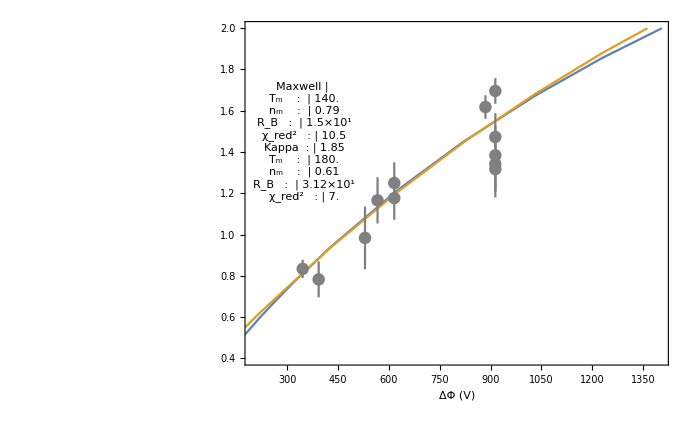

```mathematica
JVInitFitPlot2=Show[Plot[{kInitialFit2[pot],gInitialFit2[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"",""},{"ΔΦ (V)",Style[StringForm["Interval `1` (`2`)",interval,initTitle2],Bold,titleSize]}},ImageSize->700,FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable2,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData2,PlotStyle->Gray]]
```

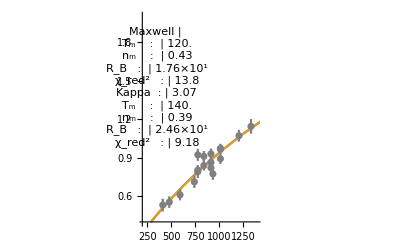

```mathematica
JVInitFitPlot1=Show[Plot[{kInitialFit1[pot],gInitialFit1[pot]},{pot,20,10000},PlotRange->plotRange,Epilog->Inset[JVParTable1,Scaled[{0.14,0.65}]],FrameTicks->All,PlotRangePadding->.1],ErrorListPlot[jErrData1,PlotStyle->Gray]]
```

```mathematica
JVInitFitPlot1=Plot[{kInitialFit1[pot],gInitialFit1[pot]},{pot,20,10000},PlotRange->plotRange,Epilog->Inset[JVParTable1,Scaled[{0.14,0.65}]],FrameTicks->All,PlotRangePadding->.1,Epilog->Point[jErrData2[[;;,1]]]]
```

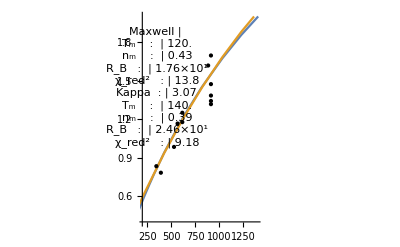

```mathematica
JVInitFitPlot2=Plot[{kInitialFit2[pot],gInitialFit2[pot]},{pot,20,10000},PlotRange->plotRange,Epilog->{PointSize[Large],Point[jErrData[[;;,1]]],Inset[JVParTable1,Scaled[{0.14,0.65}]]},FrameTicks->All,PlotRangePadding->.1]
```